#### 1)

```mathematica
f=1/x+(x^3)^(1/4);
g=ArcSin[x]/Tan[x];
h=Log[(x+1)/(x^2+1)];
D[f,x]
D[g,x]
D[h,x]//Simplify
```

-1/x^2+(3 x^2)/(4 (x^3)^(3/4))

Cot[x]/(√(1-x^2))-ArcSin[x] Csc[x]^2

-(-1+2 x+x^2)/(1+x+x^2+x^3)

#### 2)

-6 x-3 x^2+8 x^3+6 x^4

-6-6 x+24 x^2+24 x^3

{{x→-1},{x→-1/2},{x→1/2}}

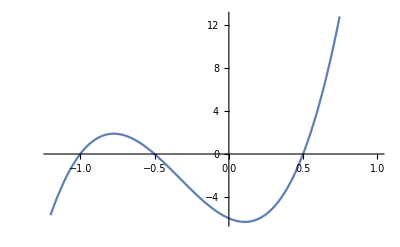

6 x^4+8 x^3-3 x^2-6 x

```mathematica
(x+1)(4 x^2-1)//Expand;
Integrate[%,x]6//Expand
%//TeXForm
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-1.2,1}]
```

#### 3)

```mathematica
6/(1+2I)+(5I)/(2-I)
(z-1+2I)(z-1-2I)//Expand
```

1/5-(2 ⅈ)/5

5-2 z+z^2

#### 4)

```mathematica
2/(x+1)-1/(x-2)//Together;
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]
%%//TeXForm
```

(-5+x)/(-2-x+x^2)

-Log[2-x]+2 Log[1+x]

\frac{x-5}{x^2-x-2}

#### 5)

3-2 x-x^2

{{x→-3},{x→1}}

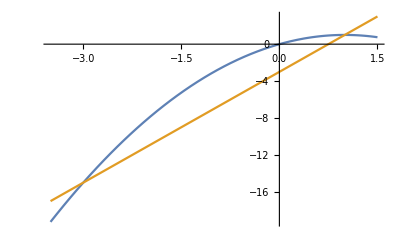

32/3

```mathematica
(1-x)(x+3)//Expand
y1=2x-x^2;
y2=4x-3;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-3.5,1.5}]
Integrate[y1-y2,{x,-3,1}]
```

#### 6)

```mathematica
A1={{1,2,2},{2,3,1},{-3,2,4}};
Det[A1]
X1={3,-1,2};
B1=A1.X1
Solve[A1.{{x},{y},{z}}==B1,{x,y,z}]
```

14

{5,5,-3}

{{x→3,y→-1,z→2}}

#### 7)

-5+4 x

3

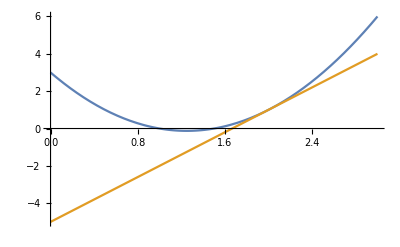

-5+3 x

```mathematica
f1[x_]:=2 x^2-5x+3;
f1'[x]
x0=2;
f1'[x0]
g1[x_]:=f1'[x0](x-x0)+f1[x0];
Plot[{f1[x],g1[x]},{x,0,3}]
g1[x]//Expand
```

#### 8)

Dany jest trojkat ABC, A(), B(), C(). Wyznacz kosinus kata BAC, pole tego trojkata oraz dlugosc wysokosci opuszczonej na bok AB.

```mathematica
u1={2,-2,1};
v1={3,0,4};
A1={2,3,3};
B1=A1+u1
C1=A1+v1
Dot[u1,v1]/(Norm[u1]Norm[v1])
Cross[u1,v1]
Norm[%]/2
Solve[%==1/2Norm[u1] h,h]
```

{4,1,4}

{5,3,7}

2/3

{-8,-5,6}

(5 √5)/2

{{h→(5 √5)/3}}